```mathematica
(* Standard *)
```

```mathematica
x2[k_,m_]:=ArcSin[(π(1+4m))/(2k-1)]
```

```mathematica
x2[1,-3]//N
```

-1.5708+4.23556 ⅈ

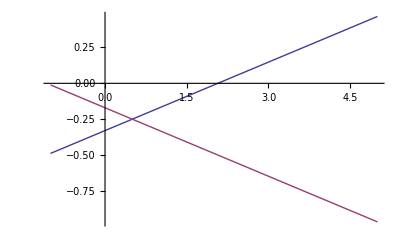

```mathematica
Plot[{(2k-1-π)/(4π),(1-π-2k)/(4π)},{k,-1,5}]
```

```mathematica
x2[2.2,0]
```

1.17841

```mathematica
plot1[k_,n_]:=Plot[{Sin[x],(4(π n - x))/(2k-1)},{x,0,2π},PlotRange->{-2,2}]
```

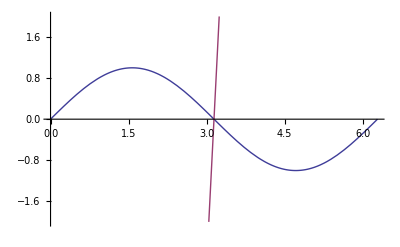

```mathematica
plot1[0.4,1]
```

```mathematica
x21[k_,n_]:=x/.FindRoot[Sin[x]==(4(π n-x))/(2k-1),{x,0.7}]
```

```mathematica
x21[0.7,0]
```

0.

```mathematica
(* Kicked rotor function *)
```

```mathematica
f[x_,k_]:={Mod[x[[1]]+k Sin[x[[1]]]+x[[2]],2π], Mod[k Sin[x[[1]]]+x[[2]],2π]}
```

```mathematica
FindRoot[f[f[x,1],1]==x,{x,{1.6,2.6}}]
```

Part::partd: Part specification x ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification x ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part will be suppressed during this calculation.

{x→{1.32812,2.65624}}

```mathematica
f[{1.3281216461540066,2.6562432923080133},1]
```

{4.95506,3.62694}

```mathematica
Plot3D[f[{x,y},1],{x,0,2π},{y,0,2π}]
```

-Graphics3D-

```mathematica
Plot3D[f[f[{x,y},1],1],{x,0,2π},{y,0,2π}]
```

-Graphics3D-

```mathematica
f0[x_,k_]:={x[[1]]+k Sin[x[[1]]]+x[[2]], k Sin[x[[1]]]+x[[2]]}
```

```mathematica
Solve[f0[{x0,y0},k]=={x0,y0},{x0,y0}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y0→0,x0→0}}

```mathematica
Solve[f0[f0[{x0,y0},k],k]=={x0,y0},{x0,y0}]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -2 ArcCos[Cos[y0]] - ArcCos[Cos[k Sin[x0]]] == 0.

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

Solve[{x0+2 y0+2 k Sin[x0]+k Sin[x0+y0+k Sin[x0]],y0+k Sin[x0]+k Sin[x0+y0+k Sin[x0]]}=={x0,y0},{x0,y0}]

```mathematica
f0[f0[{x0,p0},k],k]
```

{2 p0+x0+2 k Sin[x0]+k Sin[p0+x0+k Sin[x0]],p0+k Sin[x0]+k Sin[p0+x0+k Sin[x0]]}

```mathematica
Solve[Sin[a]==-Sin[a-b],a]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a→-ArcCos[-(√(1+2 Cos[b]+Cos[b]^2))/(√(1+2 Cos[b]+Cos[b]^2+Sin[b]^2))]},{a→ArcCos[-(√(1+2 Cos[b]+Cos[b]^2))/(√(1+2 Cos[b]+Cos[b]^2+Sin[b]^2))]},{a→-ArcCos[(√(1+2 Cos[b]+Cos[b]^2))/(√(1+2 Cos[b]+Cos[b]^2+Sin[b]^2))]},{a→ArcCos[(√(1+2 Cos[b]+Cos[b]^2))/(√(1+2 Cos[b]+Cos[b]^2+Sin[b]^2))]}}

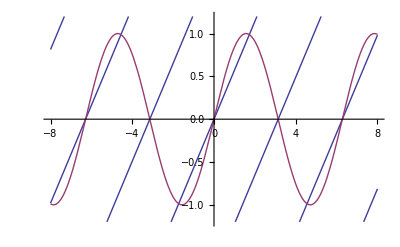

```mathematica
Plot[{Table[4/7(x-π n),{n,-10,10}],Sin[x]},{x,-8,8},PlotRange->{-1.2,1.2}]
```

```mathematica
FindRoot[x==7/4 Sin[x],{x,1}]
```

{x→1.72833}

```mathematica
(* With mod? *)
```

```mathematica
f2[x_,p_,k_]:=f[f[{x,p},k],k]
```

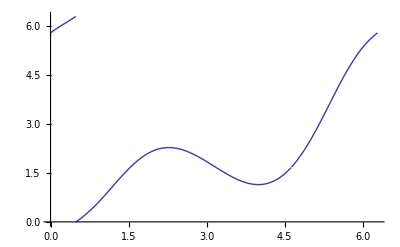

```mathematica
Plot[f2[x,2.656,1][[1]],{x,0,2π}]
```

```mathematica
f2[2,2.656,1]
```

{2.18961,2.9075}

```mathematica
f2[x,p,k]
```

{Mod[Mod[p+k Sin[x],2 π]+Mod[p+x+k Sin[x],2 π]+k Sin[Mod[p+x+k Sin[x],2 π]],2 π],Mod[Mod[p+k Sin[x],2 π]+k Sin[Mod[p+x+k Sin[x],2 π]],2 π]}

```mathematica
Mod[Mod[4.2,1],1]
```

0.2

```mathematica
Mod[34.2+23.11,2π]
```

0.761332

```mathematica
Mod[34.2,2π]+Mod[23.11,2π]
```

7.04452

```mathematica
FullSimplify[Mod[Mod[x,1],1]]
```

Mod[x,1]

```mathematica
FullSimplify[Mod[x+Mod[y,1],1]]
```

Mod[x+y,1]

```mathematica
FullSimplify[eq1[k,n]]
```

2 n π==2 Mod[n π+1/2 k Sin[x]+k Sin[n π+x+1/2 k Sin[x]],2 π]+k Sin[x]

```mathematica
7.044517542563312+0.7613322353837262
```

7.80585

```mathematica
eq1[k_,n_]:=Mod[Mod[k/2 Sin[x]+π n,2π]+k Sin[x+k/2 Sin[x]+π n],2π]==-k/2 Sin[x]+π n
```

```mathematica
eq1[k_,n_]:=n π==Mod[n π+1/2 k Sin[x]+k Sin[n π+x+1/2 k Sin[x]],2 π]+k/2 Sin[x]
```

```mathematica
FindRoot[eq1[1,1],{x,4.9}]
```

{x→4.95506}

```mathematica
g[x_,k_]:=k/2 Sin[x]+π+k Sin[x+k/2 Sin[x]+π]
```

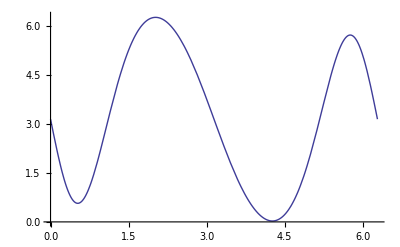

```mathematica
Plot[g[x,3.5],{x,0,2π},PlotRange->{0,2π}]
```

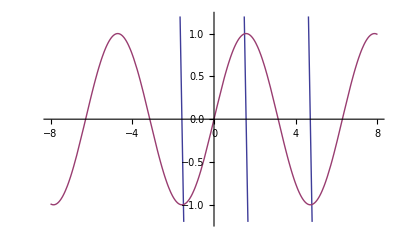

```mathematica
Plot[{Table[4/0.3(-x-π/2+π m),{m,0,2}],Sin[x]},{x,-8,8},PlotRange->{-1.2,1.2}]
```

```mathematica
FindRoot[1/4 Sin[x]+x==π/2,{x,1}]
```

{x→1.32812}

```mathematica
FindRoot[1/4 Sin[x]+x==(3π)/2,{x,1}]
```

{x→4.95506}

```mathematica
π-1/2 Sin[1.3281216461540064]
```

2.65624

```mathematica
π-1/2 Sin[4.955063661025583]
```

3.62694

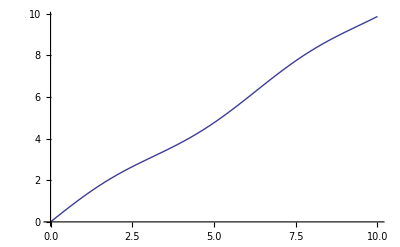

```mathematica
Plot[1/4 Sin[x]+x,{x,0,10}]
```

```mathematica
D[g[x,k],x]
```

```mathematica
FindRoot[{1/2 k Cos[x]-k (1+1/2 k Cos[x]) Cos[x+1/2 k Sin[x]]==0,g[x,k]==0},{x,2},{k,3.5}]
```

{x→0.472605,k→4.13348}

```mathematica
FindRoot[{1/2 k Cos[x]-k (1+1/2 k Cos[x]) Cos[x+1/2 k Sin[x]]==0,g[x,k]==0},{x,4},{k,3.5}]
```

{x→4.26549,k→3.512}

```mathematica
(* Check *)
```

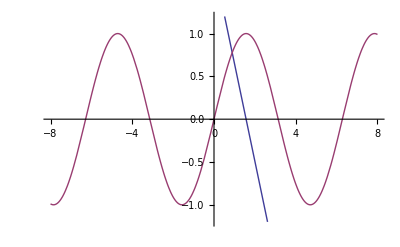

```mathematica
Plot[{4/3.5(π/2-x),Sin[x]},{x,-8,8},PlotRange->{-1.2,1.2}]
```

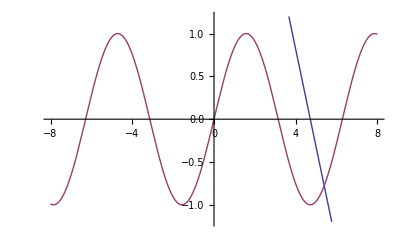

```mathematica
Plot[{4/3.5((3π)/2-x),Sin[x]},{x,-8,8},PlotRange->{-1.2,1.2}]
```